```mathematica
Manipulate[
Module[{L,Ts1,k,h1,h2,Ts2,t},
L=0.003;(*m*)
Ts1=36;(*°C*)
k=0.2;(*W/m/K*)
(*Tsurr=-15;(*°C*)*)
h1=25;(*calm W/m/°C*)
h2=14.8*(v)^0.69;(*h2=65;*)(*windy*)
Ts2[h_]=(Tsurr+k/(h*L)*Ts1)/(1+k/(h*L));
t=1/(Max[Ts1,Ts2[h1],Ts2[h2]]+5);

Graphics[{
{FaceForm[{RGBColor[1.,0.65,0.5],Opacity[0.3]}],Rectangle[{0,0.05},{0.5,0.95}]},
{FaceForm[RGBColor[1.,0.65,0.5]],Rectangle[{-0.05,0},{0,1}],Rectangle[{0.5,0},{0.55,1}]},
{Thick,
Line[{{-0.05,t*Ts1},{0,t*Ts1}}],
{Dashed,Line[{{0,t*Ts1},{0.5,t*Ts2[h1]}}]},Line[{{0.5,t*Ts2[h1]},{0.55,t*Ts2[h1]}}],
Line[{{0,t*Ts1},{0.5,t*Ts2[h2]}}],Line[{{0.5,t*Ts2[h2]},{0.55,t*Ts2[h2]}}]},
Text[Style[Row[{Subscript[Style["T",Italic],"s,1"]," = ",Ts1,"°C"}],15],{-0.15,t*Ts1}](*,
Text[Style[Row[{Subscript[Style["T",Italic],"s,2"]," = "Ts2[h1],"°C  (calm day)"}],15],{0.55,t*Ts2[h1]},{-1,0}]*)
},ImageSize->{470,375}]
],
{{v,8,"wind speed (m/s)"},1,20,1,Appearance->"Labeled"},
{{Tsurr,-15,"air temperature (°C)"},-20,10,1,Appearance->"Labeled"}]
```

```mathematica
14.8*(3)^0.69
```

31.5846

```mathematica
(*Plot[{k*(Ts1-Ts2[h1])/x,k*(Ts1-Ts2[h2])/x},{x,0,0.003},PlotStyle->{{Thick,Black},{Thick,Blue}},Frame->True]*)
```

```mathematica
Table[i,{i,0,0.003,0.0005}]
```

{0.,0.0005,0.001,0.0015,0.002,0.0025,0.003}

```mathematica
Table[(-1)^j,{j,1,7}]
```

{-1,1,-1,1,-1,1,-1}

```mathematica
Manipulate[
Graphics[BezierCurve[Table[{i,-(-1)^i},{i,0,m}],SplineDegree->n]],
{{n,4,"spline degree"},1,10,1,Appearance->"Labeled"},
{{m,20,""},1,100,1,Appearance->"Labeled"}]
```

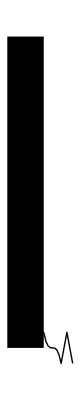

```mathematica
Graphics[{
{Rectangle[{-0.1,0},{0,1}]},
BezierCurve[Table[{i/63,0.05*(-1)^i},{i,0,5}],SplineDegree->2]
}]
```

```mathematica
Table[{i,-(-1)^i},{i,0,63}]
```

{{0,-1},{1,1},{2,-1},{3,1},{4,-1},{5,1},{6,-1},{7,1},{8,-1},{9,1},{10,-1},{11,1},{12,-1},{13,1},{14,-1},{15,1},{16,-1},{17,1},{18,-1},{19,1},{20,-1},{21,1},{22,-1},{23,1},{24,-1},{25,1},{26,-1},{27,1},{28,-1},{29,1},{30,-1},{31,1},{32,-1},{33,1},{34,-1},{35,1},{36,-1},{37,1},{38,-1},{39,1},{40,-1},{41,1},{42,-1},{43,1},{44,-1},{45,1},{46,-1},{47,1},{48,-1},{49,1},{50,-1},{51,1},{52,-1},{53,1},{54,-1},{55,1},{56,-1},{57,1},{58,-1},{59,1},{60,-1},{61,1},{62,-1},{63,1}}

```mathematica
10.45-8.333+10*√8.333
```

30.9839

```mathematica
8.6*√8.333
```

24.8256

```mathematica
12.1*√8.333
```

34.929

```mathematica
65/√8.333
```

22.5171

```mathematica
14.8*(8.333)^0.69
```

63.9167

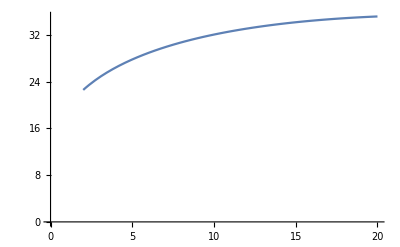

```mathematica
Plot[10.45-v+10*√v,{v,2,20},AxesOrigin->{0,0}]
```